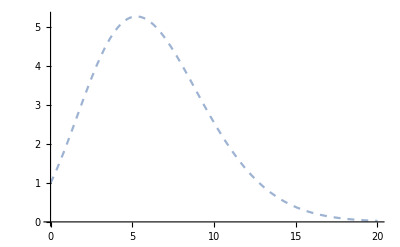

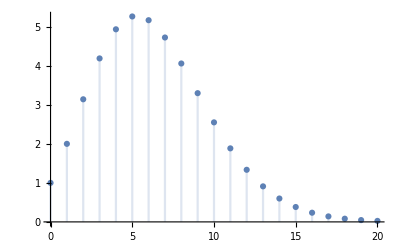

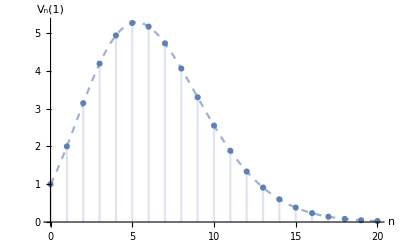

```mathematica
fp=Plot[π^(n/2)/Gamma[1+n/2],{n,0,20},PlotStyle->{Opacity[0.6],Dashed}]
gp=DiscretePlot[π^(n/2)/Gamma[1+n/2],{n,0,20}]
Show[fp,gp,AxesLabel->{Style["n",24],Style["V_n(1)",24]}]
fp=Plot[(2*π^(n/2))/Gamma[n/2],{n,0,20},PlotStyle->{Opacity[0.6],Dashed}]
gp=DiscretePlot[(2*π^(n/2))/Gamma[n/2],{n,0,20}]
Show[fp,gp,AxesLabel->{Style["n",24],Style["S_n(1)",24]}]
```

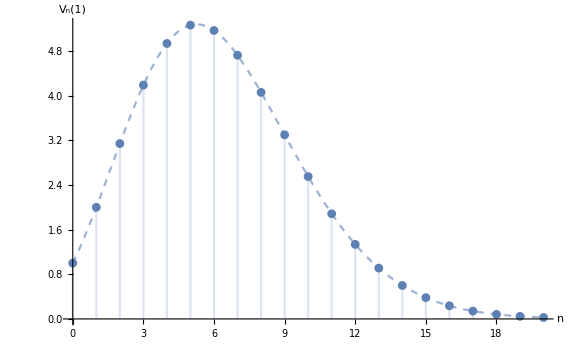

```mathematica
Show[%9,ImageSize->Large]
```

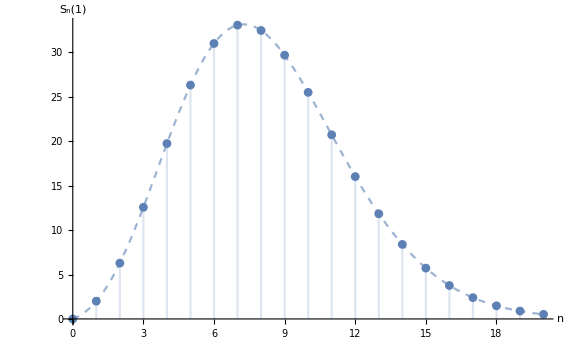

```mathematica
Show[%12,ImageSize->Large]
```